## Constantes

```mathematica
h=4.135667696*10^(-15); (*eV s*)
ℏ=6.582119569*10^(-16); (*eV s*)
c=3*^17 ;(*nm s^-1*)
omega=Range[0,10,0.01];
```

## Funciones generales

```mathematica
(*Función que devuelve la parte real y la imaginaria de la función dieléctrica a partir del índice de refracción*)
```

```mathematica
epsRe[parteRe_,parteIm_,x_]:=parteRe[x]^2-parteIm[x]^2;
epsIm[parteRe_,parteIm_,x_]:=(2*parteRe[x]*parteIm[x]);
(*Función para encontrar los máximos alrededor de intervalos dados*)
ω0i[eps_,intervalos_]:=GoldenSearchMax[eps,##]&@@@intervalos;
(*Lorentziana*)
lorentz[ω_,ω0_,γ_]:=(γ/2)^2/((ω-ω0)^2+(γ/2)^2)
(*Definición de 5 lorentzianas*)

lorentzSum[ω_,A1_,ω01_,γ1_,A2_,ω02_,γ2_,A3_,ω03_,γ3_,A4_,ω04_,γ4_,A5_,ω05_,γ5_,A6_,ω06_,γ6_]:=A1 lorentz[ω,ω01,γ1]+A2 lorentz[ω,ω02,γ2]+A3 lorentz[ω,ω03,γ3]+A4 lorentz[ω,ω04,γ4]+A5 lorentz[ω,ω05,γ5];
```

## Concentración 28.7 g/dL

```mathematica
(*Se van a importar los datos de la parte real e imaginaria del índice de refracción*)
datos0Im=Import["C:\\Users\\Poh\\Documents\\Tesis\\Refractive index\\28.7_k_ImN_Erythrocytes.csv"];
datos0Re=Import["C:\\Users\\Poh\\Documents\\Tesis\\Refractive index\\28.7_n_ReN_Erythrocytes.csv"];
(*Se eliminan los encabezados de los datos*)
datos1Im=Drop[datos0Im,1];
datos1Re=Drop[datos0Re,1];
(*Se pasa de longitudes de onda a energías y se toma a la primera columna como el vector de energías*)
datos2Im=h c/datos1Im[[All,1]];
datos2Re=h c/datos1Re[[All,1]];
(*Se interpolan los datos de la parte imaginaria y real*)
parteIm=Interpolation[Transpose[{datos2Im,datos1Im[[All,2]]}]];
parteRe=Interpolation[Transpose[{datos2Re,datos1Re[[All,2]]}]];
(*Se definen la parte real e imaginaria de la función dieléctrica*)
```

```mathematica
energias=Range[1.19,4.82,0.01];
```

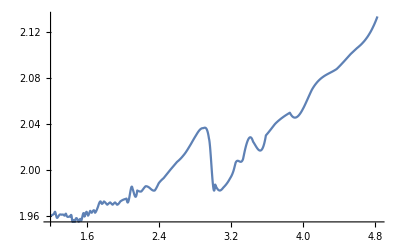

```mathematica
Plot[{epsRe[parteRe,parteIm,x]},{x,1.19,4.83},PlotRange->All]
```

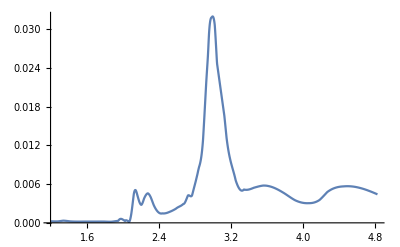

```mathematica
Plot[{epsIm[parteRe,parteIm,x]},{x,1.19,4.83},PlotRange->All]
```

```mathematica
(*Intervalos de búsqueda de los máximos*)
intervalos28={{2.1,2.2},{2.2,2.4},{2.8,3.3},{3.5,3.8},{4,4.7}};
eps28[x_]:=epsIm[parteRe,parteIm,x];
ω0i28=ω0i[eps28,intervalos28];
```

```mathematica
ω0i28
```

{2.13396,2.27349,2.72655,2.99459,3.56451,4.49601}

InterpolatingFunction::dmval: Input value {4.83329} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {4.84329} lies outside the range of data in the interpolating function. Extrapolation will be used.

NonlinearModelFit::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

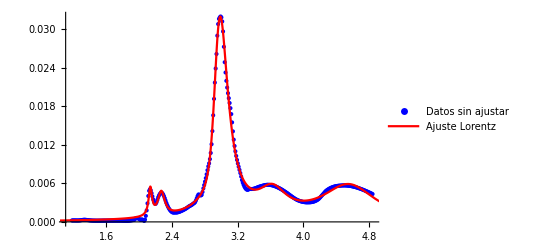

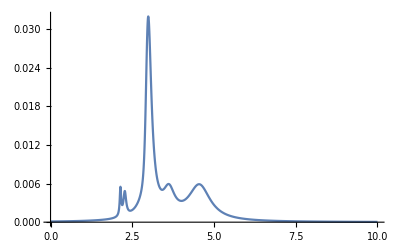

```mathematica
(*Ajuste de la parte imaginaria con lorentzianas*)
{xmin,xmax}={Min[datos2Im],Max[datos2Im]};
(*Datos para ajuste*)
eps28Data=Table[{x,eps28[x]},{x,xmin,xmax,0.01}];
(* Ajustar con NonlinearModelFit*)
fit28=NonlinearModelFit[eps28Data,lorentzSum[ω,A1,ω01,γ1,A2,ω02,γ2,A3,ω03,γ3,A4,ω04,γ4,A5,ω05,γ5],{{A1,0.01},{ω01,ω0i28[[1]]},{γ1,0.1},{A2,0.01},{ω02,ω0i28[[2]]},{γ2,0.1},{A3,0.01},{ω03,ω0i28[[3]]},{γ3,0.05},{A4,0.01},{ω04,ω0i28[[4]]},{γ4,0.1},{A5,0.01},{ω05,ω0i28[[5]]},{γ5,0.1}},ω];

(*Grafica datos originales y ajuste con 5 Lorentzianas*)
Show[ListPlot[eps28Data,PlotStyle->Blue,PlotLegends->{"Datos sin ajustar"},PlotRange->All],Plot[fit28[ω],{ω,xmin-0.5,xmax+0.5},PlotStyle->{Thick,Red},PlotLegends->{"Ajuste Lorentz"},PlotRange->All]]
Plot[fit28[ω],{ω,0,10},PlotRange->All]
```

Set::setraw: Cannot assign to raw object {0.,0.01,0.02,0.03,0.04,0.05,0.06,0.07,0.08,0.09,«991»}.

Set::setraw: Cannot assign to raw object 0.000101259.

Set::setraw: Cannot assign to raw object 0.000101824.

General::stop: Further output of StyleBox[RowBox[{\"Set\", \"::\", \"setraw\"}], \"MessageName\"] will be suppressed during this calculation.

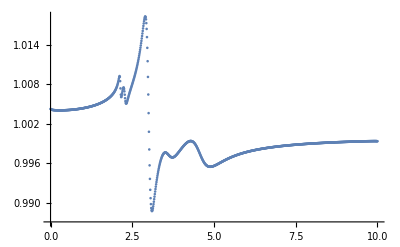

```mathematica
(*Obtención de la parte real a partir de la parte imaginaria con KK*)
parteIm028=Table[fit28[x],{x,0,10,0.01}];
parteReKK128=kkrebook[omega,parteIm028];
ListPlot[Transpose[{omega,parteReKK128}],PlotRange->All]
```

Set::setraw: Cannot assign to raw object {0.,0.01,0.02,0.03,0.04,0.05,0.06,0.07,0.08,0.09,«991»}.

Set::setraw: Cannot assign to raw object {1.00427,1.00422,1.00418,1.00415,1.00414,1.00412,1.00411,1.0041,1.0041,1.00409,«991»}.

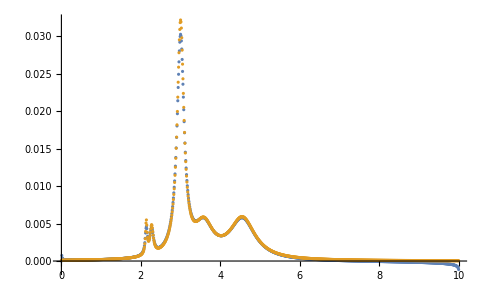

```mathematica
(*Obtención de la parte imaginaria a partir de la real obtenida con KK*)
parteImKK128=kkimbook[omega,parteReKK128];
ListPlot[{Transpose[{omega,parteImKK128}],Transpose[{omega,parteIm028}]},PlotRange->All]
```

```mathematica
eps28KK=selfconsbook[omega,parteReKK1,parteIm028,10,0.5];
```

Set::setraw: Cannot assign to raw object {0.,0.01,0.02,0.03,0.04,0.05,0.06,0.07,0.08,0.09,«991»}.

Set::setraw: Cannot assign to raw object {1.00427,1.00422,1.00418,1.00415,1.00414,1.00412,1.00411,1.0041,1.0041,1.00409,«991»}.

Set::setraw: Cannot assign to raw object 0.000101259.

General::stop: Further output of Set::setraw will be suppressed during this calculation.

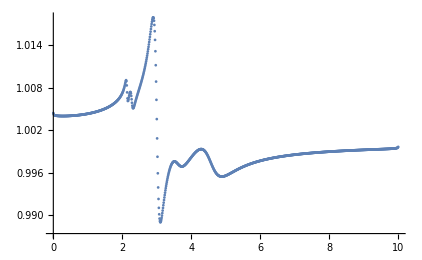

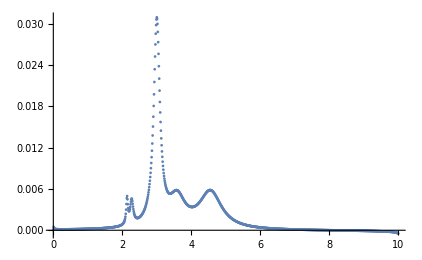

```mathematica
ListPlot[{Transpose[{omega,eps28KK[[1]]}]},PlotRange->All]
ListPlot[{Transpose[{omega,eps28KK[[2]]}]},PlotRange->All]
```

## Concentración 32 g/dL

```mathematica
(*Se van a importar los datos de la parte real del índice de refracción y del coeficiente de absorción*)
datos0re=Import["C:\\Users\\Poh\\Documents\\Tesis\\Refractive index\\32_n_ReN_Erythrocytes.csv"];
datosuA=Import["C:\\Users\\Poh\\Documents\\Tesis\\Refractive index\\32_uA_Erythrocytes.csv"];
(*Se eliminan los encabezados de los datos*)
datos1re=Drop[datos0re,1];
datos1uA=Drop[datosuA,1];
(*Se pasa de longitudes de onda a energías y se toma a la primera columna como el vector de energías*)
datos2re=h c/datos1re[[All,1]];
datos2im=h c/datos1uA[[All,1]];
(*Obtener la parte imaginariad del índice de refracción a partir del coeficiente de absorción*)
datos3im=datos1uA[[All,2]]*10^(-6)*datos1uA[[All,1]]/(4*Pi);
(*Se interpolan los datos de la parte real e imaginaria*)
parteRe32=Interpolation[Transpose[{datos2re,datos1re[[All,2]]}]];
parteIm32=Interpolation[Transpose[{datos2im,datos3im}]];
```

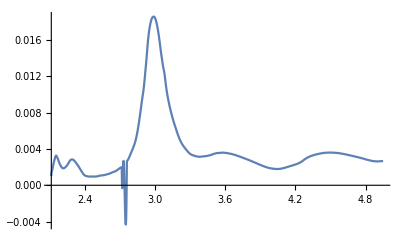

```mathematica
Plot[parteIm32[x],{x,2.11,4.95},PlotRange->All]
```

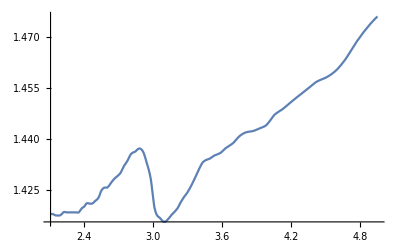

```mathematica
Plot[parteRe32[x],{x,2.11,4.95}]
```

```mathematica
(*Intervalos de búsqueda de los máximos*)
intervalos32={{2,2.1},{2.15,2.3},{2.8,3.2},{3.4,3.7},{4.2,4.7}};
eps32[x_]:=epsIm[parteRe32,parteIm32,x];
ω0i32=ω0i[eps32,intervalos32];
```

InterpolatingFunction::dmval: Input value {2.0382} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {2.0618} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

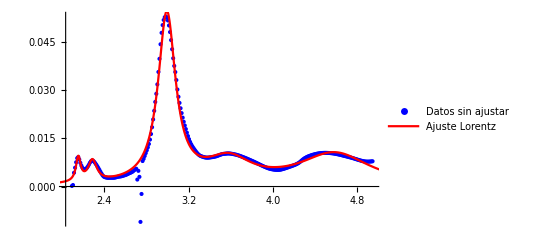

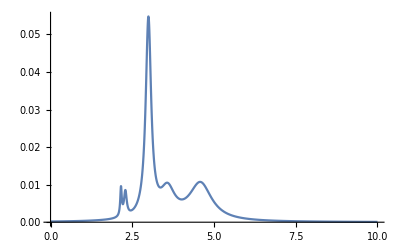

```mathematica
(*Ajuste de la parte imaginaria con lorentzianas*)
{xmin32,xmax32}={Min[datos2im],Max[datos2im]};
(*Datos para ajuste*)
eps32Data=Table[{x,eps32[x]},{x,xmin32,xmax32,0.01}];
(* Ajustar con NonlinearModelFit*)
fit32=NonlinearModelFit[eps32Data,lorentzSum[ω,A1,ω01,γ1,A2,ω02,γ2,A3,ω03,γ3,A4,ω04,γ4,A5,ω05,γ5],{{A1,0.01},{ω01,ω0i32[[1]]},{γ1,0.05},{A2,0.01},{ω02,ω0i32[[2]]},{γ2,0.1},{A3,0.01},{ω03,ω0i32[[3]]},{γ3,0.1},{A4,0.01},{ω04,ω0i32[[4]]},{γ4,0.1},{A5,0.01},{ω05,ω0i32[[5]]},{γ5,0.1}},ω];

(*Grafica datos originales y ajuste con 5 Lorentzianas*)
Show[ListPlot[eps32Data,PlotStyle->Blue,PlotLegends->{"Datos sin ajustar"},PlotRange->All],Plot[fit32[ω],{ω,xmin-0.5,xmax+0.5},PlotStyle->{Thick,Red},PlotLegends->{"Ajuste Lorentz"},PlotRange->All]]
Plot[fit32[ω],{ω,0,10},PlotRange->All]
```

Set::setraw: Cannot assign to raw object {0.,0.01,0.02,0.03,0.04,0.05,0.06,0.07,0.08,0.09,«991»}.

Set::setraw: Cannot assign to raw object 0.000187363.

Set::setraw: Cannot assign to raw object 0.000188387.

General::stop: Further output of Set::setraw will be suppressed during this calculation.

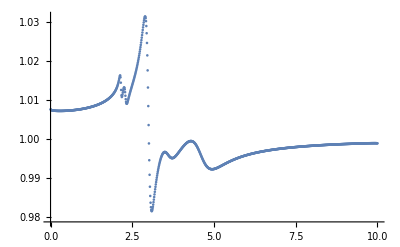

```mathematica
(*Obtención de la parte real a partir de la parte imaginaria con KK*)
parteIm032=Table[fit32[x],{x,0,10,0.01}];
parteReKK132=kkrebook[omega,parteIm032];
ListPlot[Transpose[{omega,parteReKK132}],PlotRange->All]
```

Set::setraw: Cannot assign to raw object {0.,0.01,0.02,0.03,0.04,0.05,0.06,0.07,0.08,0.09,«991»}.

Set::setraw: Cannot assign to raw object {1.00757,1.00748,1.0074,1.00736,1.00733,1.0073,1.00728,1.00726,1.00725,1.00724,«991»}.

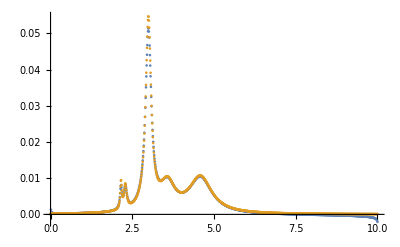

```mathematica
(*Obtención de la parte imaginaria a partir de la real obtenida con KK*)
parteImKK132=kkimbook[omega,parteReKK132];
ListPlot[{Transpose[{omega,parteImKK132}],Transpose[{omega,parteIm032}]},PlotRange->All]
```

```mathematica
eps32KK=selfconsbook[omega,parteReKK132,parteIm032,10,0.5];
```

Set::setraw: Cannot assign to raw object {0.,0.01,0.02,0.03,0.04,0.05,0.06,0.07,0.08,0.09,«991»}.

Set::setraw: Cannot assign to raw object {1.00757,1.00748,1.0074,1.00736,1.00733,1.0073,1.00728,1.00726,1.00725,1.00724,«991»}.

Set::setraw: Cannot assign to raw object 0.000187363.

General::stop: Further output of Set::setraw will be suppressed during this calculation.

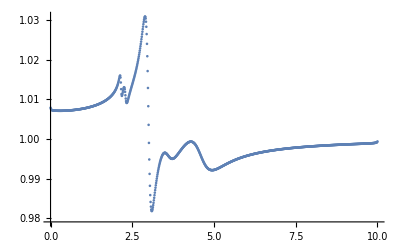

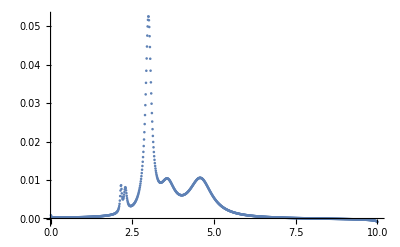

```mathematica
ListPlot[{Transpose[{omega,eps32KK[[1]]}]},PlotRange->All]
ListPlot[{Transpose[{omega,eps32KK[[2]]}]},PlotRange->All]
```

## Concentración 30.6 g/dL

```mathematica
(*Se van a importar los datos de la parte real del índice de refracción y del coeficiente de absorción*)
```

```mathematica
datos0re30=Import["C:\\Users\\Poh\\Documents\\Tesis\\Refractive index\\30.6_n_ReN_Erythrocytes.csv"];
datosuA30=Import["C:\\Users\\Poh\\Documents\\Tesis\\Refractive index\\30.6_uA_Erythrocytes.csv"];
(*Se eliminan los encabezados de los datos*)
datos1re30=Drop[datos0re30,1];
datos1uA30=Drop[datosuA30,1];
(*Se pasa de longitudes de onda a energías y se toma a la primera columna como el vector de energías*)
datos2re30=h c/datos1re30[[All,1]];
datos2im30=h c/datos1uA30[[All,1]];
(*Obtener la parte imaginariad del índice de refracción a partir del coeficiente de absorción*)
datos3im30=datos1uA30[[All,2]]*10^(-6)*datos1uA30[[All,1]]/(4*Pi);
(*Se interpolan los datos de la parte imaginaria*)
parteRe30=Interpolation[Transpose[{datos2re30,datos1re30[[All,2]]}]];
parteIm30=Interpolation[Transpose[{datos2im30,datos3im30}],Method->"Spline"];
```

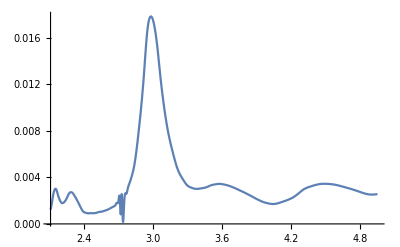

```mathematica
Plot[parteIm30[x],{x,2.11,4.95},PlotRange->All]
```

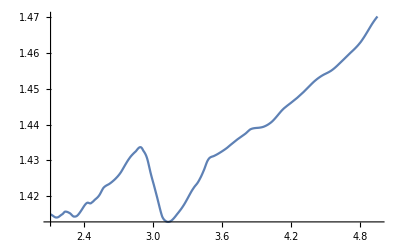

```mathematica
Plot[parteRe30[x],{x,2.11,4.95}]
```

```mathematica
(*Intervalos de búsqueda de los máximos*)
intervalos30={{2,2.1},{2.15,2.4},{2.8,3.2},{3.4,3.7},{4.2,4.7}};
eps30[x_]:=epsIm[parteRe30,parteIm30,x];
ω0i30=ω0i[eps30,intervalos30];
```

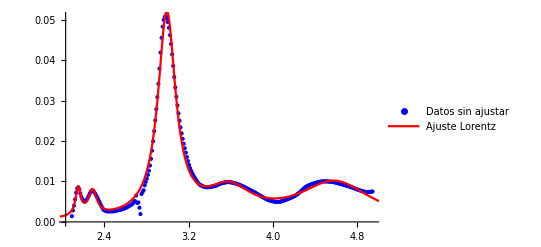

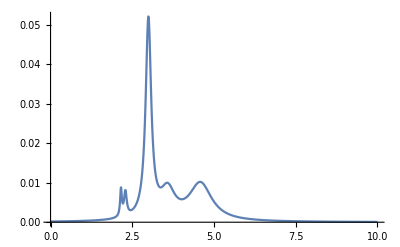

```mathematica
(*Ajuste de la parte imaginaria con lorentzianas*)
{xmin30,xmax30}={Min[datos2im30],Max[datos2im30]};
(*Datos para ajuste*)
eps30Data=Table[{x,eps30[x]},{x,xmin30,xmax30,0.01}];
(* Ajustar con NonlinearModelFit*)
fit30=NonlinearModelFit[eps30Data,lorentzSum[ω,A1,ω01,γ1,A2,ω02,γ2,A3,ω03,γ3,A4,ω04,γ4,A5,ω05,γ5],{{A1,0.01},{ω01,ω0i30[[1]]},{γ1,0.05},{A2,0.01},{ω02,ω0i30[[2]]},{γ2,0.05},{A3,0.01},{ω03,ω0i30[[3]]},{γ3,0.1},{A4,0.01},{ω04,ω0i30[[4]]},{γ4,0.1},{A5,0.01},{ω05,ω0i30[[5]]},{γ5,0.1}},ω];

(*Grafica datos originales y ajuste con 5 Lorentzianas*)
Show[ListPlot[eps30Data,PlotStyle->Blue,PlotLegends->{"Datos sin ajustar"},PlotRange->All],Plot[fit30[ω],{ω,xmin-0.5,xmax+0.5},PlotStyle->{Thick,Red},PlotLegends->{"Ajuste Lorentz"},PlotRange->All]]
Plot[fit30[ω],{ω,0,10},PlotRange->All]
```

Set::setraw: Cannot assign to raw object {0.,0.01,0.02,0.03,0.04,0.05,0.06,0.07,0.08,0.09,«991»}.

Set::setraw: Cannot assign to raw object 0.000181009.

Set::setraw: Cannot assign to raw object 0.000182001.

General::stop: Further output of Set::setraw will be suppressed during this calculation.

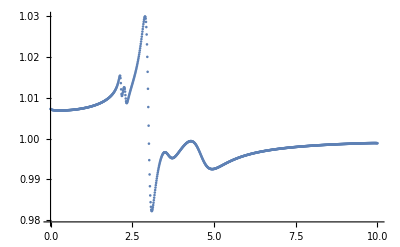

```mathematica
(*Obtención de la parte real a partir de la parte imaginaria con KK*)
parteIm030=Table[fit30[x],{x,0,10,0.01}];
parteReKK130=kkrebook[omega,parteIm030];
ListPlot[Transpose[{omega,parteReKK130}],PlotRange->All]
```

Set::setraw: Cannot assign to raw object {0.,0.01,0.02,0.03,0.04,0.05,0.06,0.07,0.08,0.09,«991»}.

Set::setraw: Cannot assign to raw object {1.00728,1.00719,1.00712,1.00708,1.00704,1.00702,1.007,1.00699,1.00697,1.00696,«991»}.

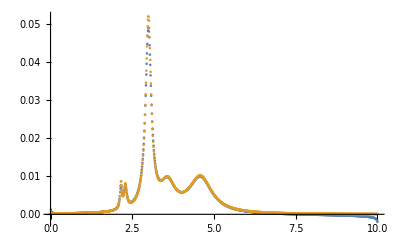

```mathematica
(*Obtención de la parte imaginaria a partir de la real obtenida con KK*)
parteImKK130=kkimbook[omega,parteReKK130];
ListPlot[{Transpose[{omega,parteImKK130}],Transpose[{omega,parteIm030}]},PlotRange->All]
```

```mathematica
eps30KK=selfconsbook[omega,parteReKK130,parteIm030,10,0.5];
```

Set::setraw: Cannot assign to raw object {0.,0.01,0.02,0.03,0.04,0.05,0.06,0.07,0.08,0.09,«991»}.

Set::setraw: Cannot assign to raw object {1.00728,1.00719,1.00712,1.00708,1.00704,1.00702,1.007,1.00699,1.00697,1.00696,«991»}.

Set::setraw: Cannot assign to raw object 0.000181009.

General::stop: Further output of Set::setraw will be suppressed during this calculation.

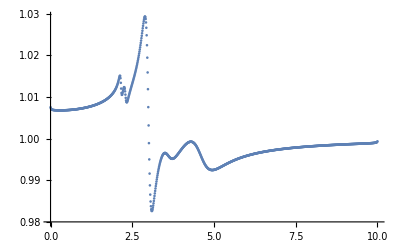

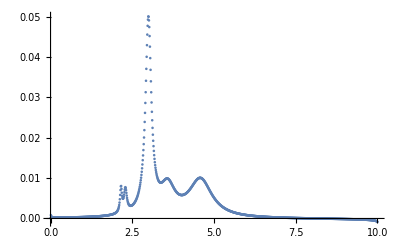

```mathematica
ListPlot[{Transpose[{omega,eps30KK[[1]]}]},PlotRange->All]
ListPlot[{Transpose[{omega,eps30KK[[2]]}]},PlotRange->All]
```

## Comparación entre concentraciones

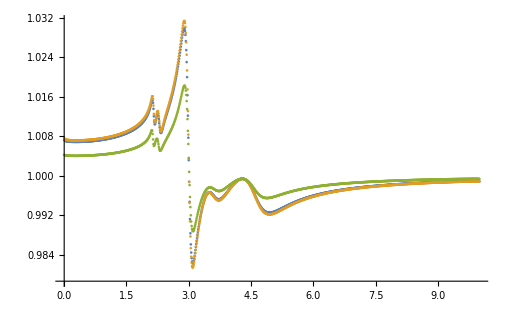

```mathematica
ListPlot[{Transpose[{omega,eps28KK[[1]]}],Transpose[{omega,eps32KK[[1]]}],Transpose[{omega,eps30KK[[1]]}]},PlotRange->All]
```

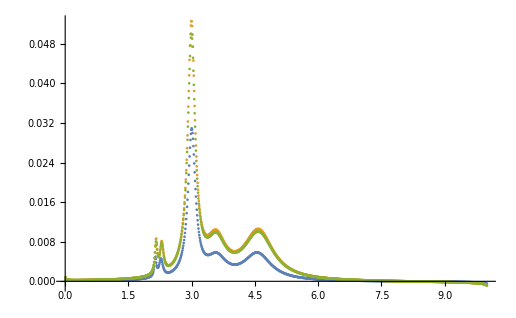

```mathematica
ListPlot[{Transpose[{omega,eps28KK[[2]]}],Transpose[{omega,eps32KK[[2]]}],Transpose[{omega,eps30KK[[2]]}]},PlotRange->All]
```

## Plasma